## Allpass lattice transfer function (from Effect Design, part I by Jon Dattorro)

```mathematica
A[z_,β_,γ_]:=(β + γ(1+β)/z + 1/z^2)/(1 + γ(1+β)/z + β/z^2)
```

β controls the Q of the filter :

```mathematica
β[ωc_,Q_]:=(1-Tan[ωc/(2 Q)])/(1+Tan[ωc/(2 Q)])
```

And γ controls the cutoff frequency:

```mathematica
γ[ωc_]:=-Cos[ωc]
```

We can now write the transfer function of the allpass filter in terms of ωc and Q:

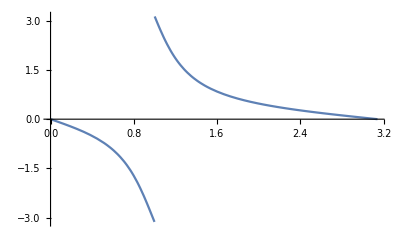

```mathematica
AωQ[z_,ωc_,Q_]:=A[z,β[ωc,Q],γ[ωc]]

zz[ω_]:=ⅇ^(ⅈ ω)
Plot[Arg[AωQ[zz[ω],1,2]],{ω,0,π}]
```

## Skirt height control

If we mix the unfiltered input with the allpass filtered output we get a filter like a resonator with adjustable skirt height.

```mathematica
AdjSkirt[z_,ωc_, Q_,skirtHeight_,bellHeight_]:= allpassGain AωQ[z,ωc, Q] + unfilteredGain
```

Since the second order allpass filter transfer function has zero phase shift at zero and Nyquist, the height of the skirt is the sum of the mixing coefficients of the Allpass filtered signal and the unfilitered signal.

Since the allpass filter has 180 degree phase shift at the cutoff frequency, the height of the bell is the difference of the allpass mixing coefficient and the unfilitered signal mixing coefficient.

```mathematica
(* apg = allpass gain; ufg = unfiltered gain *)
Solve[sh == apg + ufg && bh == apg-ufg,{apg,ufg}]
```

{{apg→(bh+sh)/2,ufg→1/2 (-bh+sh)}}

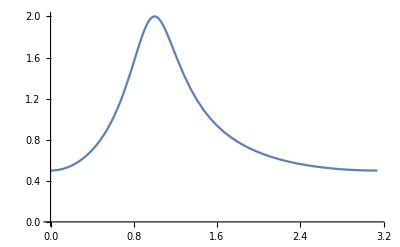

```mathematica
AdjSkirt[z_,ωc_, Q_,sh_,bh_]:= (1/2)((bh + sh) AωQ[z,ωc, Q] + (sh - bh))

Plot[Abs[AdjSkirt[zz[ω],1,2,0.5,2]],{ω,0,π},PlotRange->{0,2}]
```

## Test the method before porting to C

```mathematica
bellSkirt[z_,ωc_,Q_,bg_, sg_]:=Module[{apb0, apb1,apb2,apa0,apa1,apa2,mixb0,mixb1,mixb2,beta,gamma,apg,ufg},

(* beta controls the Q *)
beta = β[ωc,Q];

(* gamma controls the centre frequency *)
gamma = γ[ωc];

(* allpass filtered gain *)
apg = (bg+sg)/2;

(* unfiltered gain *)
ufg=(bg-sg)/2;

(* allpass filter coefficients *)
apb0=beta;
apb1=gamma*(1.0+beta);
apb2=1.0;
apa0=1.0;
apa1=gamma*(1.0+beta);
apa2=beta;

(* b coefficients for mixture of allpass filtered and unfiltered signal *)
mixb0=apg*apb0+ufg*apa0;
mixb1=apg*apb1+ufg*apa1;
mixb2=apg*apb2+ufg*apa2;

(* output the transfer function *)
(mixb0 + mixb1/z + mixb2/z^2)/(apa0 + apa1/z + apa2/z^2)
]

Plot[Abs[bellSkirt[zz[ω],1,2,0.5,2]],{ω,0,π},PlotRange->{0,2}]
```

-Graphics-